# Infinite 3D medium, Isotropic Point Source, Isotropic Scattering

## Exponential Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3Disopointisoscatter`"]
```

inf3Disopointisoscatter`

## Util

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

### Diffusion modes

```mathematica
diffusionMode[v_,d_,r_]:=(2 π)^(-d/2) r^(1-d/2) v^(-1-d/2) BesselK[1/2 (-2+d),r/v]
```

## Analytic solutions

### Caseology quantities

```mathematica
CaseN0[c_,v0_]:=1/2 c v0^3 (c/(v0^2-1)-1/v0^2)
```

```mathematica
Casev0[c_?NumericQ]:=FindRoot[c v ArcTanh[1/v]-1==0,{v,1.00000000001,10^10},Method->"Brent"][[1]][[2]]
```

```mathematica
Casev0approx[c_]:=1/√(1-c^(2.4429445001914587+0.5786368322364553/c-0.021581332427913873 c))
```

```mathematica
CaseN[c_,v_]:=v (Caseλ[v,c]^2+((π c v)/2)^2)
```

```mathematica
Caseλ[v_,c_]:=1-c v ArcTanh[v]
```

### Fluence: exact solution (1)

[Bothe 1942]

```mathematica
ϕexact1a[r_,Σt_,c_]:=1/(2 Pi^2 r)NIntegrate[(z ArcTan[z/Σt])/(z-c Σt  ArcTan[z/Σt])Sin[r z],{z,0,Infinity},Method->"ExtrapolatingOscillatory"]
```

[Case et al. 1953]

```mathematica
ϕexact1b[r_,Σt_,c_]:=Exp[-Σt r]/(4 Pi r^2)+c Σt/(2 Pi^2 r)NIntegrate[ArcTan[z]^2/(z-c ArcTan[z])Sin[r Σt z],{z,0,Infinity},Method->"LevinRule"]
```

### Rigorous diffusion approximation

```mathematica
ϕrigourousDiffusion[r_,Σt_,c_]:=Σt/(4 Pi r)E^(-r Σt/#)/(# CaseN0[c,#])&[Casev0[c]]
```

```mathematica
ϕtransient[r_,Σt_,c_]:=Σt/(4 Pi r)NIntegrate[ⅇ^(-Σt r /v)/(v CaseN[c,v]),{v,0,1}]
```

Expansion of transient term [Case et al. 1953]

```mathematica
ϕtransient2[r_,Σt_,c_,M_]:=Exp[-r Σt]/(4 Pi r^2)+1/(4 Pi r)Sum[ExpIntegralE[2n,r Σt]SeriesCoefficient[v/CaseN[c,v],{v,0,2n}],{n,1,M}]
```

### Fluence: exact solution (2)

[Davison 1947]

```mathematica
ϕexact2a[r_,Σt_,c_]:=ϕrigourousDiffusion[r,Σt,c]+Σt/(4 Pi r)NIntegrate[ⅇ^(-Σt r y)/((c^2 π^2)/(4 y^2)+(1-c/(2y)Log[(y+1)/(y-1)])^2),{y,1,Infinity}]
```

[Case and Zwiefel 1967]

```mathematica
ϕexact2b[r_,Σt_,c_]:=ϕrigourousDiffusion[r,Σt,c]+Σt/(4 Pi r)NIntegrate[ⅇ^(-Σt r /v)/(v CaseN[c,v]),{v,0,1}]
```

### n-th scattered fluence

```mathematica
ϕexact1[r_,Σt_,c_,n_]:=(c Σt)^n/(2 π^2 r)NIntegrate[(ArcTan[z/Σt]^(1+n) Sin[r z])/z^n,{z,0,Infinity},Method->"ExtrapolatingOscillatory"]
```

```mathematica
ϕexact2[r_,Σt_,c_,n_]:=(c^n Σt)/(2^(n+3)Pi^2 I r)Chop[NIntegrate[Exp[-r z Σt]/z^n((Log[(z+1)/(z-1)]+I Pi)^(n+1)-(Log[(z+1)/(z-1)]-I Pi)^(n+1)),{z,1,Infinity}]]
```

```mathematica
ϕGaussian[r_,Σt_,c_,n_]:=(3 √3 ⅇ^(-(3 r^2 Σt^2)/(4 (1+n))) c^n Σt^2)/(8 √((1+n)^3) π^(3/2))
```

### Moments

```mathematica
ϕm[c_,Σt_,m_?IntegerQ,n_]:=Limit[Simplify[(-1)^(m/2)((2 Gamma[(3+m)/2])/Gamma[(1+m)/2] D[((c Σt ArcTan[z/Σt])/z)^(1+n)/(c Σt),{z,m}])],z->0]
```

```mathematica
TableForm[Table[ϕm[c,Σt,m,n],{m,0,6,2}]]
```

c^n/Σt
(2 c^n (1+n))/Σt^3
(4 c^n (1+n) (18+5 n))/(3 Σt^5)
(8 c^n (1+n) (810+343 n+35 n^2))/(9 Σt^7)

```mathematica
ϕm[c_,Σt_,m_?IntegerQ]:=Limit[Simplify[(-1)^(m/2)((2 Gamma[(3+m)/2])/Gamma[(1+m)/2] D[ArcTan[z/Σt]/(z-c Σt ArcTan[z/Σt]),{z,m}])],z->0]
```

```mathematica
TableForm[Table[ϕm[c,Σt,m],{m,0,6,2}]]
```

1/(Σt-c Σt)
2/((-1+c)^2 Σt^3)
(8 (-9+4 c))/(3 (-1+c)^3 Σt^5)
(16 (135-144 c+44 c^2))/(3 (-1+c)^4 Σt^7)

Recurrence derivation [Case et al. 1953]

```mathematica
CaseB[0,c_]:=1/(1-c);
CaseB[m_,c_]:=1/(1-c)^2 Sum[Caseb[m,s](c/(1-c))^(s-1),{s,1,m}];
Caseb[m_,1]:=1/(2m+1);
Caseb[m_,s_]:=Sum[Caseb[n,s-1]/(1+2(m-n)),{n,s-1,m-1}]
```

```mathematica
ϕmCase[c_,Σt_,m_?IntegerQ]:=1/Σt^(m+1)CaseB[m/2,α]Factorial[m+1]
```

```mathematica
TableForm[Table[FullSimplify[ϕmCase[c,Σt,m]],{m,0,6,2}]]
```

1/(Σt-α Σt)
2/((-1+α)^2 Σt^3)
(8 (-9+4 α))/(3 (-1+α)^3 Σt^5)
(16 (135+4 α (-36+11 α)))/(3 (-1+α)^4 Σt^7)

### Classical diffusion approximation

```mathematica
ϕDiffusion[r_,Σt_,c_]:=1/(Σt(1-c))diffusionMode[1/(√(3(1- c)) Σt),3,r]
```

```mathematica
FullSimplify[ϕDiffusion[r,Σt,c],Assumptions->0<c<1&&Σt>0]
```

(3 ⅇ^(-√(3-3 c) r Σt) Σt)/(4 π r)

### Grosjean-style diffusion approximation

```mathematica
ϕGrosjean[r_,Σt_,c_]:=Exp[-r Σt]/(4 Pi r^2)+c/(Σt(1-c))diffusionMode[(√(2-c))/(√(3(1- c)) Σt),3,r]
```

```mathematica
FullSimplify[ϕGrosjean[r,Σt,c],Assumptions->0<c<1&&Σt>0]
```

(ⅇ^(-r Σt)-(3 c ⅇ^(-√(3+3/(-2+c)) r Σt) r Σt)/(-2+c))/(4 π r^2)

### Angular ϕ Integral

Note: this form leaves out the singular term e^(-r Σ_t)/(4 π r^2)δ(u-1), because it doesn’t plot:

```mathematica
Lintegral[r_,u_,Σt_,c_,ϕ_]:=(c Σt)/(4 Pi)NIntegrate[ϕ[√(r^2+t^2-2 r t u),Σt,c]Exp[-Σt t],{t,0,Infinity}]
```

### Angular Classical diffusion approximation

```mathematica
Ldiffusion[r_,u_,Σt_,c_]:=1/(4 Pi)ϕDiffusion[r,Σt,c]+1/(4 Pi)u(3 ⅇ^(-r √(3-3 c) Σt)  (1+r √(3-3 c) Σt))/(4 π r^2)
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_isotropicscatter*"];
```

```mathematica
index[x_]:=Module[{data,α,Σt},
data=Import[x,"Table"];
Σt=data[[1,13]];
α=data[[2,3]];
{α,Σt,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
mfps=Union[#[[2]]&/@simulations]
```

{0.3,1}

```mathematica
numcollorders=simulations[[1]][[3]][[2,13]];
maxr=simulations[[1]][[3]][[2,5]];dr=simulations[[1]][[3]][[2,7]];
numr=Floor[maxr/dr];
```

## Select simulation

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

## Compare Deterministic and MC

### Mean Track Length

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
meanTL=data[[-1]]
mfp/(1-c)
```

{Mean,track,length:,1.11109}

1.11111

### Fluence - Exact solution (1a) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

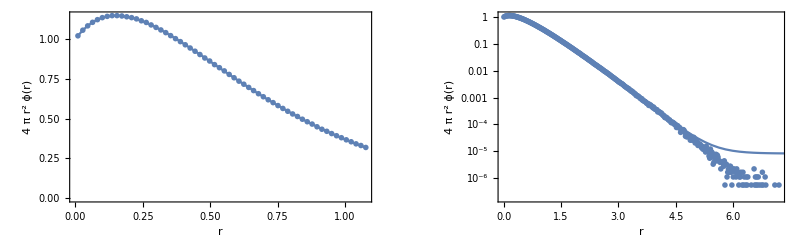

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsCR=ppoints[data[[4]],dr,maxr];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact1a[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact1a[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (1a)\nInfinite 3D, isotropic point source, isotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Fluence - Exact solution (1b) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

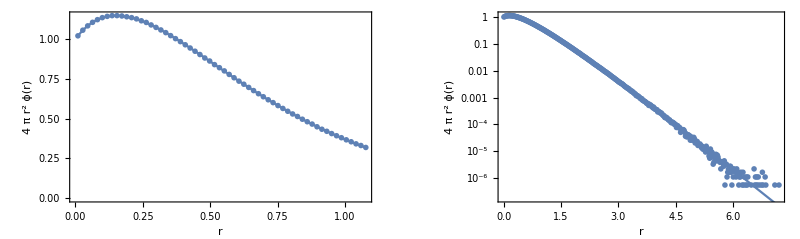

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsCR=ppoints[data[[4]],dr,maxr];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact1b[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact1b[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (1b)\nInfinite 3D, isotropic point source, isotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Fluence - Exact solution (2a) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

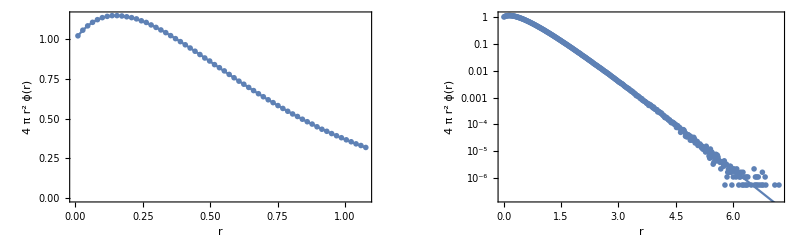

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsCR=ppoints[data[[4]],dr,maxr];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact2a[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact2a[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (2a)\nInfinite 3D, isotropic point source, isotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Fluence - Exact solution (2b) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

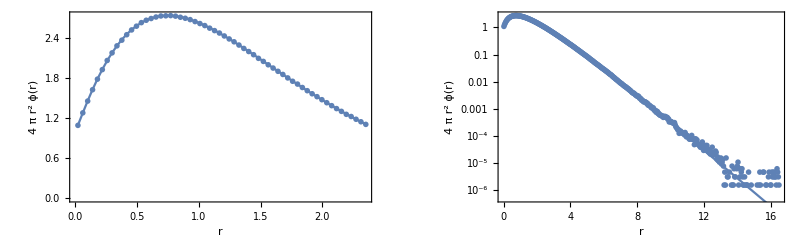

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsCR=ppoints[data[[4]],dr,maxr];
pointsFluence=ppoints[data[[6]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact2b[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact2b[#[[1]],1/mfp,c]}]& /@pointsCR[[1;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (2b)\nInfinite 3D, isotropic point source, isotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Fluence - Diffusion approximations (Classical and Grosjean) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

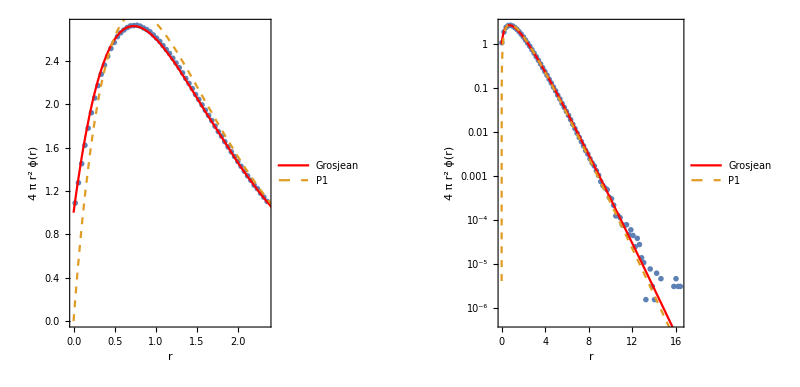

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[{
4 Pi r^2  ϕGrosjean[r,1/mfp,c],
4 Pi r^2  ϕDiffusion[r,1/mfp,c]
}
,{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Grosjean","P1"},{0.5,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence[[1;;-1;;5]],PlotRange->All,PlotStyle->PointSize[.01]],
LogPlot[{
4 Pi r^2  ϕGrosjean[r,1/mfp,c],
4 Pi r^2  ϕDiffusion[r,1/mfp,c]
}
,{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Grosjean","P1"},{0.3,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Diffusion Approximations\nInfinite 3D, isotropic point source, isotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Fluence - Diffusion approximation (Rigorous) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

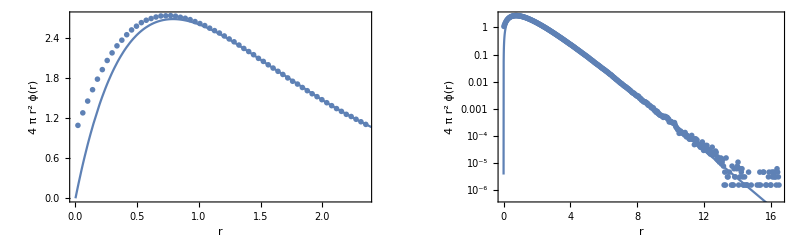

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
pointsFluence=ppoints[data[[6]],dr,maxr];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[4 Pi r^2  ϕrigourousDiffusion[r,1/mfp,c],{r,0,maxr},PlotRange->All],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
LogPlot[4 Pi r^2 ϕrigourousDiffusion[r,1/mfp,c],{r,0,maxr},PlotRange->All],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Rigorous Diffusion Approximation\nInfinite 3D, isotropic point source, isotropic scattering, fluence ϕ[r], c = "<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

## N-th order fluence / scalar flux

### N-th collided Fluence - Exact solution (1) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set collision order","collisionOrder = "<>ToString[#]:>(collisionOrder=#;)&/@Range[0,numcollorders-1]],Dynamic[collisionOrder]}}
```

{{Set c,},{Set mfp,},{Set collision order,}}

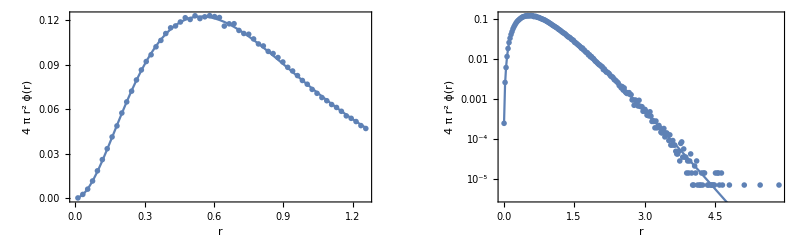

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluencei=3 numcollorders+15+collisionOrder;

pointsFluence=ppoints[data[[fluencei]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact1[#[[1]],1/mfp,c,collisionOrder]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact1[#[[1]],1/mfp,c,collisionOrder]}]& /@pointsFluence[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (1)\nInfinite 3D medium, isotropic point source, isotropic scattering, n-th scattered fluence ϕ[r|"<>ToString[collisionOrder]<>"], c ="<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### N-th collided Fluence - Exact solution (2) comparison to MC

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set collision order","collisionOrder = "<>ToString[#]:>(collisionOrder=#;)&/@Range[0,numcollorders-1]],Dynamic[collisionOrder]}}
```

{{Set c,},{Set mfp,},{Set collision order,}}

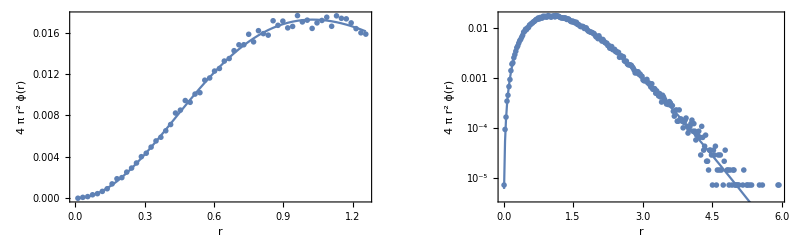

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluencei=3 numcollorders+15+collisionOrder;

pointsFluence=ppoints[data[[fluencei]],dr,maxr];
exact1FluenceShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact2[#[[1]],1/mfp,c,collisionOrder]}]& /@pointsFluence[[1;;60]];
exact1Fluence=Quiet[{#[[1]],4 Pi (#[[1]])^2 ϕexact2[#[[1]],1/mfp,c,collisionOrder]}]& /@pointsFluence[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1FluenceShallow,PlotRange->All,Joined->True],
ListLogPlot[exact1Fluence,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Exact solution (2)\nInfinite 3D medium, isotropic point source, isotropic scattering, n-th scattered fluence ϕ[r|"<>ToString[collisionOrder]<>"], c ="<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### N-th collided Fluence - Approximations

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set collision order","collisionOrder = "<>ToString[#]:>(collisionOrder=#;)&/@Range[0,numcollorders-1]],Dynamic[collisionOrder]}}
```

{{Set c,},{Set mfp,},{Set collision order,}}

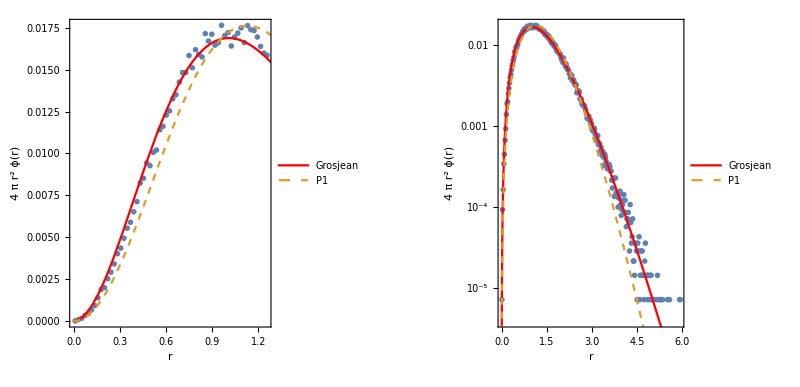

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluencei=3 numcollorders+15+collisionOrder;

pointsFluence=ppoints[data[[fluencei]],dr,maxr];
seriesclassical=c^collisionOrder SeriesCoefficient[ϕDiffusion[r,1/mfp,C],{C,0,collisionOrder}];
seriesG=c^collisionOrder SeriesCoefficient[ϕGrosjean[r,1/mfp,C],{C,0,collisionOrder}];
plotϕshallow=Quiet[Show[
ListPlot[pointsFluence[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[{4 Pi r^2 seriesG,4 Pi r^2 seriesclassical},{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Grosjean","P1"},{0.5,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[pointsFluence,PlotRange->All,PlotStyle->PointSize[.01]],
LogPlot[{4 Pi r^2 seriesG,4 Pi r^2 seriesclassical},{r,0,maxr},PlotRange->All,PlotStyle->{Red,Dashed},PlotLegends->Placed[{"Grosjean","P1"},{0.5,.2}]],
Frame->True,
FrameLabel->{{4 Pi r^2 ϕ[r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Diffusion Approximations\nInfinite 3D medium, isotropic point source, isotropic scattering, n-th scattered fluence ϕ[r|"<>ToString[collisionOrder]<>"], c ="<>ToString[c]<>", Σ_t = "<>ToString[1/mfp]]
```

### Compare moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
nummoments=data[[2,15]];
ϕmoments={data[[10]]};
ks=Table[k,{k,0,nummoments-1}];
analytic=Table[ϕm[c,1/mfp,k],{k,ks}];
j=Join[{ks},{analytic},ϕmoments];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 6. | 6.00171
1 | 0. | 9.16206
2 | 21.6 | 21.6302
3 | 0. | 68.5295
4 | 269.568 | 272.563

### n-th collided moments of ϕ

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]},
{ActionMenu["Set collision order","collisionOrder = "<>ToString[#]:>(collisionOrder=#;)&/@Range[0,numcollorders-1]],Dynamic[collisionOrder]}}
```

{{Set c,},{Set mfp,},{Set collision order,}}

```mathematica
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
nummoments=data[[2,15]];
ϕmoments=N[{data[[numcollorders+13+collisionOrder]]}];
ks=Table[k,{k,0,nummoments-1}];
analytic=Table[ϕm[c,1/mfp,k,collisionOrder],{k,ks}];
j=Join[{ks},{analytic},ϕmoments];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 0.03125 | 0.031262
1 | 0.+0. ⅈ | 0.094565
2 | 0.375 | 0.374203
3 | 0. | 1.83103
4 | 10.75 | 10.681

### Angular Distributions

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

```mathematica
depthi=52
```

52

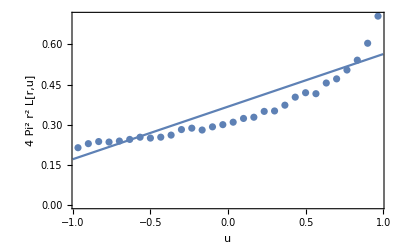

```mathematica
Clear[u];
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
du=data[[2,9]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluxi=17+4 numcollorders+Floor[maxr/dr];
angularFlux =ppointsu[data[[fluxi+depthi]],du,1];
r = dr * depthi-0.5 dr;
Show[
ListPlot[angularFlux,PlotRange->All,
Frame->True,
FrameLabel->{{"4 Pi^2 r^2 L[r,u]",},{u,}}],
Plot[4 Pi r^2 Pi Ldiffusion[r,u,1/mfp,c],{u,-1,1},PlotRange->All]
]
```

### Angular Distribution: Integral of Grosjean’s Diffusion Approximation

```mathematica
{{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]},{ActionMenu["Set mfp","mfp = "<>ToString[#]:>(mfp=#;)&/@mfps],Dynamic[mfp]}}
```

{{Set c,},{Set mfp,}}

```mathematica
depthi=52
```

52

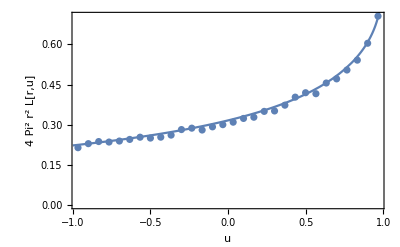

```mathematica
Clear[u];
data=SelectFirst[simulations,#[[1]]==c&&#[[2]]==mfp&][[3]];
du=data[[2,9]];
maxr=data[[2,5]];
dr=data[[2,7]];
fluxi=17+4 numcollorders+Floor[maxr/dr];
angularFlux =ppointsu[data[[fluxi+depthi]],du,1];
r = dr * depthi-0.5 dr;
Show[
ListPlot[angularFlux,PlotRange->All,
Frame->True,
FrameLabel->{{"4 Pi^2 r^2 L[r,u]",},{u,}}],
Plot[4 Pi r^2 Pi  Lintegral[r,u,1/mfp,c,ϕGrosjean],{u,-1,1},PlotRange->All]
]
```

## End context

```mathematica
End[]
```